```mathematica
Exit[]
```

```mathematica
Get["/data/mapk/mapk01.mx"];
Get["/home/abergman/dicty/SPSA.m"]
ParallelEvaluate[$KernelID]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16}

```mathematica
{v,θ0}={{p2, p3a, p3b, p3c, p3d, p4, p5, StotNative, StotOE}, {10.0, 0.01, 0.9, 300, 0.005, 1.0, 0.01, 3., 3000}};
```

```mathematica
θ0={56.70995318158104,0.7832247267456027,0.09889924756473911,5.292187714746446,0.000018875209270420096,0.3404435189016253,0.023315554320830257,2,30};
```

```mathematica
pθ:=Thread[Rule[v,θ0]];
Grid[List@@#&/@pθ//Transpose,Frame->All]
slevel:={StotNative,StotOE}/.pθ
```

p2 | p3a | p3b | p3c | p3d | p4 | p5 | StotNative | StotOE
56.71 | 0.783225 | 0.0988992 | 5.29219 | 0.0000188752 | 0.340444 | 0.0233156 | 2 | 30

```mathematica
dX=0.005;
X=Range[0.1,1.0,0.01]
Length[X]
```

{0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99,1.}

91

```mathematica
grad=1.5Range[0.0,1.0,0.25]
Length[grad]
```

{0.,0.375,0.75,1.125,1.5}

5

```mathematica
inputs0=Flatten@Outer[Times,X,grad];
inputs1=Flatten@Outer[Times,X+dX,grad];
```

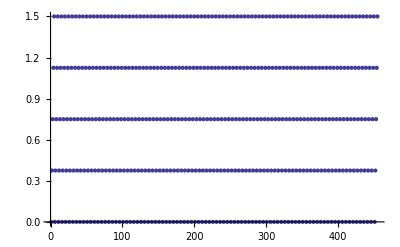

```mathematica
(inputs1-inputs0)/dX//ListPlot
```

```mathematica
p3sigmoid=Function[s,p3[s]->(p3b-p3d)/(1+Exp[p3c(Smem[s][t]-p3a)])+p3d]/@{0,1};
```

```mathematica
ListPlot3D[Partition[inputs0,Length[grad]]]
```

-Graphics3D-

```mathematica
dat=Table[
dat=ParallelTable[
plist=Flatten@Join[{Stot->s,p1[0]->p5*inputs0[[d]],p1[1]->p5*inputs1[[d]],p3sigmoid,Di->0.0001}/.pθ,pθ];
runsim[plist]
,{d,Length@inputs0}];
Partition[dat,Length[grad]]
,{s,slevel}];
```

```mathematica
MI=MAPKpp[1]-MAPKpp[0]/.dat;
Dimensions[MI]
```

{2,91,5}

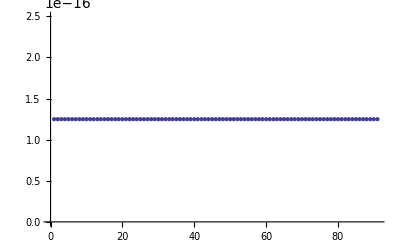

```mathematica
ListPlot[MI[[1,All,1]]]
```

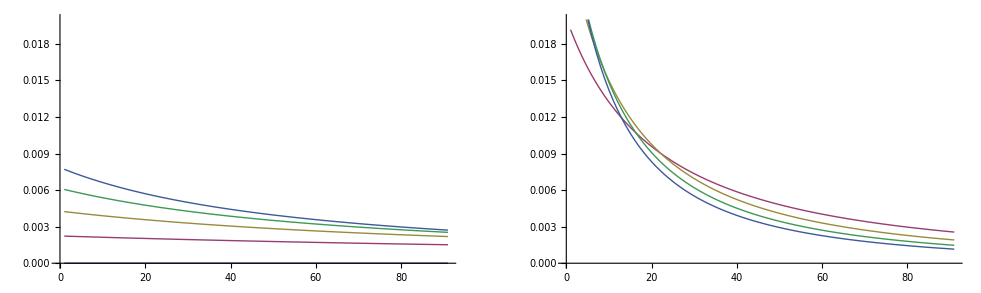

```mathematica
Block[{pr={0,0.02}},
GraphicsRow[{ListLinePlot[(Transpose@MI[[1]])/dX,PlotRange->pr],ListLinePlot[(Transpose@MI[[2]])/dX,PlotRange->pr]}]
]
```

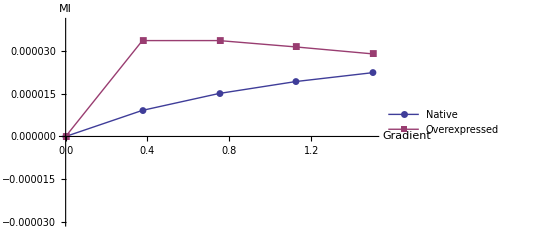

```mathematica
ListLinePlot[Map[{grad,#}ᵀ&,Mean[MAPKpp[1]-MAPKpp[0]/.Transpose@dat]],PlotMarkers->Automatic,PlotLegends->LineLegend[{"Native","Overexpressed"}],AxesLabel->{"Gradient","MI"},PlotRange->10^-5{-3,4}]
```